```mathematica
(*Define alpha function based on m and n using Piecewise*)Alpha[m_,n_]:=Piecewise[{{(-1)^m,n==1},{(-1)^(m+1)*m^2,n==2},{(-1)^(m+n-1)*2^(n-2)*m*Sum[Binomial[n+k-3,k-1]*Product[m-j,{j,k,n+k-3}],{k,1,m-n+2}],n≥3}}]
```

```mathematica
Alpha[4,2]
```

-16

```mathematica
(*Define Fourier transform of Chebyshev polynomials using Alpha function*)
FourierTn[m_,lambda_]:=Sum[Alpha[m,n]*(Exp[I*lambda]/(I*lambda)^n+(-1)^(n+m)*Exp[-I*lambda]/(I*lambda)^n),{n,1,m+1}]

(*Define the inner product with respect to J0(t)*)
InnerProduct[f_,g_]:=Integrate[f[t]*Conjugate[g[t]]*BesselJ[0,t],{t,-Infinity,Infinity}]

(*Initialize list for orthogonal functions*)
orthogonalFunctions={};

(*Gram-Schmidt process*)
For[n=0,n<1,n++,(*Use only first 4 terms for demonstration*)(*Compute function to be orthogonalized*)fn[t_]:=FourierTn[n,t];
(*Orthogonalize*)newFunc[t_]=fn[t]-Sum[InnerProduct[fn,g]/InnerProduct[g,g]*g[t],{g,orthogonalFunctions}];
(*Normalize*)normalizedNewFunc[t_]=newFunc[t]/Sqrt[InnerProduct[newFunc,newFunc]];
(*Add to list*)AppendTo[orthogonalFunctions,normalizedNewFunc]]

(*Print orthogonal functions*)
orthogonalFunctions
```

$Aborted

{}

```mathematica
f[t]
```

f[t]

```mathematica
NIntegrate[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi))*BesselJ[0,t],{t,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81037×10^7}. NIntegrate obtained -0.999997-1.35612×10^-10 ⅈ and 0.0000438801 for the integral and error estimates.

-0.999997-1.35612×10^-10 ⅈ

```mathematica
NIntegrate[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi)),{t,-Infinity,Infinity}]
```

-1.+4.18887×10^-13 ⅈ

```mathematica
FullSimplify[(FourierTn[1,t]-FourierTn[0,t]/(2*Pi))/-1]
```

```mathematica
Integrate[FourierTn[2,t]-(-2 ⅈ π t Cos[t]+(2 ⅈ π+t) Sin[t])/(π t^2),{t,-Infinity,Infinity}]
```

-1-2 π

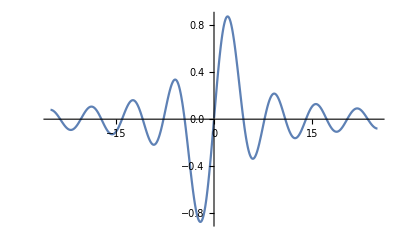

```mathematica
Plot[Im[Out[431]],{t,-25,25}]
```

```mathematica
Out[182]=Out[183]
```

Set::write: Tag Out in %182 is Protected.

(8 t Cos[t]+2 (-4+t^2) Sin[t])/t^3

```mathematica
Alpha[m,n]
```

0

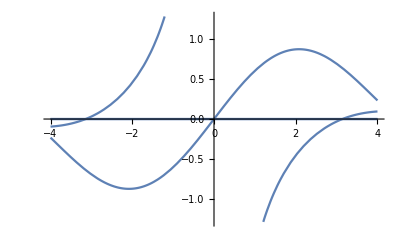

```mathematica
Plot[ReIm[{FourierTn[1,t],(2 ⅈ (-t Cos[t]+Sin[t]))/t^2}],{t,-4,4}]
```

```mathematica
(*Define symbolic inner product*)InnerProductSymbolic[f_,g_]:=NIntegrate[f*g*BesselJ[0,t],{t,-Infinity,Infinity},WorkingPrecision->20]

(*Define v1 and v2*)
v1=FourierTn[0,t];
v2=FourierTn[1,t];

(*Compute u1 by normalizing v1*)
norm1=Sqrt[InnerProductSymbolic[v1,v1]];
u1=FullSimplify[v1/norm1];

(*Compute the components for u2*)
innerProd1=InnerProductSymbolic[u1,v2];
innerProd2=InnerProductSymbolic[u1,u1];(*This should be 1 since u1 is normalized*)(*Compute u2 and normalize it*)u2Unnormalized=FullSimplify[v2-innerProd1/innerProd2*u1];
norm2=Sqrt[InnerProductSymbolic[u2Unnormalized,u2Unnormalized]];
u2=FullSimplify[u2Unnormalized/norm2];
```

NIntegrate::precw: The precision of the argument function (((ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t) BesselJ[0,t] («1»))/t) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0 and 3.1853604009017516801×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((BesselJ[0,t] (0. Cos[t]+«57» Sin[t])^2)/t^2) is less than WorkingPrecision (20.).

```mathematica
EInnerProduct[f_,g_]:=Integrate[f*Conjugate[g]*BesselJ[0,t],{t,-Infinity,Infinity}];
```

```mathematica
InnerProduct[f_,g_]:=NIntegrate[f*Conjugate[g]*BesselJ[0,t],{t,-Infinity,Infinity},WorkingPrecision->25];

u1=FourierTn[0,t]/Sqrt[InnerProduct[FourierTn[0,t],FourierTn[0,t]]];
u2=(FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1)/Sqrt[InnerProduct[FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1,FourierTn[1,t]-InnerProduct[u1,FourierTn[1,t]]*u1]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {169.6666666666666666666667}. NIntegrate obtained 8.56630437982057845236515-5.340030418682800592525036×10^-55 ⅈ and 0.0001353234488475413579434121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-255.}. NIntegrate obtained -3.398310791868838920787765×10^-54-4.531260313543484840431729×10^-39 ⅈ and 0.0001214726287964056930481408 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
u2
```

1.25658803879748240974167 ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)

```mathematica
u3Unnormalized=FourierTn[2,t]-InnerProduct[u1,FourierTn[2,t]]*u1-InnerProduct[u2,FourierTn[2,t]]*u2;
u3=u3Unnormalized/Sqrt[InnerProduct[u3Unnormalized,u3Unnormalized]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {169.6666666666666666666667}. NIntegrate obtained -1.258513886557358037936387-1.082845995188997161463038×10^-55 ⅈ and 0.00004647167864871656315327441 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {255.}. NIntegrate obtained 8.234953041881355800084101×10^-55+1.371464652394229702832499×10^-39 ⅈ and 0.00006667722272556570152728138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {169.6666666666666666666667}. NIntegrate obtained -0.637116067695483289718368+1.615937527591678573816721×10^-54 ⅈ and 0.0002036986517603810593083922 for the integral and error estimates.

```mathematica
u3
```

(1.58879086601846254900566×10^-54-1.2528258941504849248253 ⅈ) (4 (-(ⅈ ⅇ^(-ⅈ t))/t^3+(ⅈ ⅇ^(ⅈ t))/t^3)-4 (-ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2)+(0.429992876686475416073977+3.69972925569721385036517×10^-56 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)-(1.03479434924870549095566×10^-54+1.72336607783213604067049×10^-39 ⅈ) ((1.16109122742189016160454×10^-54+1.54818288303966431771355×10^-39 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)+(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)

```mathematica
NIntegrate[u3*BesselJ[0,t],{t,-Infinity,Infinity},WorkingPrecision->15]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-4.81036685170376×10^7}. NIntegrate obtained 2.23095898475326×10^-39-3.38474289865156 ⅈ and 0.0000931468373785532 for the integral and error estimates.

2.23095898475326×10^-39-3.38474289865156 ⅈ

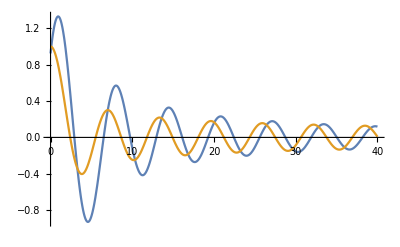

```mathematica
Plot[{Re[u1]-Im[u2]-Im[u3],BesselJ[0,t]},{t,0,40},PlotRange->All]
```

```mathematica
u3
```

```mathematica
{u1,u2,u3}
```

{0.341667 ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t),1.25655 ((-2.4883×10^-17+8.07695×10^-17 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t),(2.39752×10^-14+1.25283 ⅈ) (4 (-(ⅈ ⅇ^(-ⅈ t))/t^3+(ⅈ ⅇ^(ⅈ t))/t^3)-4 (-ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2)+(0.429991+1.41621×10^-15 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)-(1.16278×10^-14+5.23192×10^-15 ⅈ) ((-2.4883×10^-17+8.07695×10^-17 ⅈ) ((ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)+ⅇ^(-ⅈ t)/t^2-ⅇ^(ⅈ t)/t^2+(ⅈ ⅇ^(-ⅈ t))/t+(ⅈ ⅇ^(ⅈ t))/t)+(ⅈ ⅇ^(-ⅈ t))/t-(ⅈ ⅇ^(ⅈ t))/t)}

```mathematica
u1=FourierTn[0,t]/Sqrt[EInnerProduct[FourierTn[0,t],FourierTn[0,t]]];
```

$Aborted